```mathematica
transformation = LinearFractionalTransform[{{a,b,c},{e,f,g},{h,i,j}}]
PNEW = {(a x + b y + c)/(h x + i y + j),(e x + f y + g)/(h x + i y + j)}
```

TransformationFunction[(a | b | c
e | f | g
h | i | j)]

{(c+a x+b y)/(j+h x+i y),(g+e x+f y)/(j+h x+i y)}

{{0.503566,-0.482255},{3.89796,-3.66083},{-2.47967,0.840229},{-0.290723,0.497516},{1.54322,-2.05239},{1.56223,2.34232},{-0.839268,-1.38003},{1.50197,-3.68513},{-1.37436,-0.609172},{-1.80292,-0.223139},{3.34051,-3.26263},{3.19232,-0.657801},{2.5514,2.31851},{-0.207961,0.656262},{-1.43952,2.84309},{-3.02595,-0.560859},{0.401884,1.77566},{-0.615388,-2.44288},{-0.633994,-0.00751594},{-0.863249,-3.18494}}

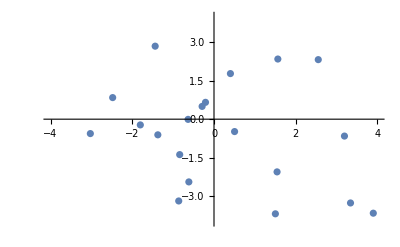

```mathematica
Shape =RandomPoint[Rectangle[{-4,-4},{4,4}],20]
ListPlot[Shape, PlotRange->{{-4,4},{-4,4}}]
```

```mathematica
Newshape = transformation[Shape]
```

{{(0.503566 a-0.482255 b+c)/(0.503566 h-0.482255 i+j),(0.503566 e-0.482255 f+g)/(0.503566 h-0.482255 i+j)},{(3.89796 a-3.66083 b+c)/(3.89796 h-3.66083 i+j),(3.89796 e-3.66083 f+g)/(3.89796 h-3.66083 i+j)},{(-2.47967 a+0.840229 b+c)/(-2.47967 h+0.840229 i+j),(-2.47967 e+0.840229 f+g)/(-2.47967 h+0.840229 i+j)},{(-0.290723 a+0.497516 b+c)/(-0.290723 h+0.497516 i+j),(-0.290723 e+0.497516 f+g)/(-0.290723 h+0.497516 i+j)},{(1.54322 a-2.05239 b+c)/(1.54322 h-2.05239 i+j),(1.54322 e-2.05239 f+g)/(1.54322 h-2.05239 i+j)},{(1.56223 a+2.34232 b+c)/(1.56223 h+2.34232 i+j),(1.56223 e+2.34232 f+g)/(1.56223 h+2.34232 i+j)},{(-0.839268 a-1.38003 b+c)/(-0.839268 h-1.38003 i+j),(-0.839268 e-1.38003 f+g)/(-0.839268 h-1.38003 i+j)},{(1.50197 a-3.68513 b+c)/(1.50197 h-3.68513 i+j),(1.50197 e-3.68513 f+g)/(1.50197 h-3.68513 i+j)},{(-1.37436 a-0.609172 b+c)/(-1.37436 h-0.609172 i+j),(-1.37436 e-0.609172 f+g)/(-1.37436 h-0.609172 i+j)},{(-1.80292 a-0.223139 b+c)/(-1.80292 h-0.223139 i+j),(-1.80292 e-0.223139 f+g)/(-1.80292 h-0.223139 i+j)},{(3.34051 a-3.26263 b+c)/(3.34051 h-3.26263 i+j),(3.34051 e-3.26263 f+g)/(3.34051 h-3.26263 i+j)},{(3.19232 a-0.657801 b+c)/(3.19232 h-0.657801 i+j),(3.19232 e-0.657801 f+g)/(3.19232 h-0.657801 i+j)},{(2.5514 a+2.31851 b+c)/(2.5514 h+2.31851 i+j),(2.5514 e+2.31851 f+g)/(2.5514 h+2.31851 i+j)},{(-0.207961 a+0.656262 b+c)/(-0.207961 h+0.656262 i+j),(-0.207961 e+0.656262 f+g)/(-0.207961 h+0.656262 i+j)},{(-1.43952 a+2.84309 b+c)/(-1.43952 h+2.84309 i+j),(-1.43952 e+2.84309 f+g)/(-1.43952 h+2.84309 i+j)},{(-3.02595 a-0.560859 b+c)/(-3.02595 h-0.560859 i+j),(-3.02595 e-0.560859 f+g)/(-3.02595 h-0.560859 i+j)},{(0.401884 a+1.77566 b+c)/(0.401884 h+1.77566 i+j),(0.401884 e+1.77566 f+g)/(0.401884 h+1.77566 i+j)},{(-0.615388 a-2.44288 b+c)/(-0.615388 h-2.44288 i+j),(-0.615388 e-2.44288 f+g)/(-0.615388 h-2.44288 i+j)},{(-0.633994 a-0.00751594 b+c)/(-0.633994 h-0.00751594 i+j),(-0.633994 e-0.00751594 f+g)/(-0.633994 h-0.00751594 i+j)},{(-0.863249 a-3.18494 b+c)/(-0.863249 h-3.18494 i+j),(-0.863249 e-3.18494 f+g)/(-0.863249 h-3.18494 i+j)}}

```mathematica
lower = -5
upper = 5
Manipulate[ListPlot[Newshape/.{a->p,b->q,c->r,e->t,f->u,g->v,h->w,i->z, j -> o},PlotRange->{{-10,10},{-10,10}}],{{p,1},lower,5}, {{q,0},lower,5}, {{r,0},-5,5},{{t,0},-5,5}, {{u,0},-5,5}, {{v,1},-5,5}, {{w,0},-5,5}, {{z,1},-5,5}, {{o,0},-5,5}]
```

-5

5